# Maximum Likelihood Inference of s and h from trios

```mathematica
SetDirectory[NotebookDirectory[]]; (*setwd()*)
```

## We define the average fitness of genotypes arising from all three informative couples (AA x Aa, Aa x Aa, Aa x aa):

```mathematica
w1[s_,h_]:=(2+h*s )/2; (* AA x Aa *)
```

```mathematica
w2[s_,h_]:=(4+2*h*s+s)/4; (* Aa x Aa *)
```

```mathematica
w3[s_,h_]:=(2+h*s+s)/2;(* Aa x aa *)
```

## Now we introduce the likelihood function where:

### c1 is the count of AA born from AA x Aa parents;

### c2 is the count of Aa born from AA x Aa parents;

### c3 is the count of AA born from Aa x Aa parents;

### c4 is the count of Aa born from Aa x Aa parents;

### c5 is the count of aa born from Aa x Aa parents;

### c6 is the count of Aa born from Aa x aa parents;

### c7 is the count of aa born from Aa x aa parents;

## The likelihood function (assuming independence among trios, offspring, and sites):

```mathematica
Lik[s_,h_]:= Multinomial[c1,c2,c3,c4,c5,c6,c7]*((1/(2*w1[s,h]))^c1)*(((1+h*s)/(2*w1[s,h]))^c2)*((1/(4*w2[s,h]))^c3)*(((1+h*s)/(2*w2[s,h]))^c4)*(((1+s)/(4*w2[s,h]))^c5)*(((1+h*s)/(2*w3[s,h]))^c6)*(((1+s)/(2*w3[s,h]))^c7);
```

```mathematica
(*We work directly (manually) in Log space to avoid underflow*)
```

```mathematica
LogLik[s_,h_]:=Log[ Multinomial[c1,c2,c3,c4,c5,c6,c7]]*(c1*Log[1/(2*w1[s,h])] + c2*Log[(1+h*s)/(2*w1[s,h])]+c3*Log[1/(4*w2[s,h])]+c4*Log[(1+h*s)/(2*w2[s,h])]+c5*Log[(1+s)/(4*w2[s,h])]+c6*Log[(1+h*s)/(2*w3[s,h])] +c7*Log[(1+s)/(2*w3[s,h])])
```

```mathematica
TraditionalForm[Lik[s,h]]
```

2^c4 (1/(h s+2))^c1 ((h s+1)/(h s+2))^c2 (1/(2 h s+s+4))^c3 ((h s+1)/(2 h s+s+4))^c4 ((s+1)/(2 h s+s+4))^c5 ((h s+1)/(h s+s+2))^c6 ((s+1)/(h s+s+2))^c7 (c1+c2+c3+c4+c5+c6+c7;c1,c2,c3,c4,c5,c6,c7)

```mathematica
TraditionalForm[LogLik[s,h]]
```

log((c1+c2+c3+c4+c5+c6+c7;c1,c2,c3,c4,c5,c6,c7)) (c1 log(1/(h s+2))+c2 log((h s+1)/(h s+2))+c3 log(1/(2 h s+s+4))+c4 log((2 (h s+1))/(2 h s+s+4))+c5 log((s+1)/(2 h s+s+4))+c6 log((h s+1)/(h s+s+2))+c7 log((s+1)/(h s+s+2)))

```mathematica
(*Dist:=ProbabilityDistribution[Lik[s,h], {s,-Infinity, 0}, {h,-1,1 }]*)
```

```mathematica
(*Integrate[Lik[s, h],{s,-Infinity, 0}, {h,-1,1 }, Assumptions->c1=100,c2=100,c3=50,c4=100,c5=50,c6=100,c7=100]*)
```

```mathematica
(*https://community.wolfram.com/groups/-/m/t/160450*)
```

## A failed attempt to find an analytical solution:

```mathematica
PDH=D[Lik[s,h],h];
```

```mathematica
PDS=D[Lik[s,h],s];
```

```mathematica
(*Solve[{PDS==0,PDH==0},{s,h},Reals]*)(*this will not finish*)
```

## Instead of solving, we plot the Log-Likelihood surfaces

#### Single SNP

```mathematica
(*TODO: use GraphicsGrid[] to show plots combined*)
(*https://mathematica.stackexchange.com/questions/207282/how-can-i-generate-an-array-of-plots-and-export-them*)
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["single_SNP/additive/strong/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];
Export["single_SNP_additive_strong_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["single_SNP/additive/moderate/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["single_SNP_additive_moderate_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["single_SNP/additive/weak/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["single_SNP_additive_weak_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["single_SNP/recessive/strong/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["single_SNP_recessive_strong_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["single_SNP/recessive/moderate/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["single_SNP_recessive_moderate_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["single_SNP/recessive/weak/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["single_SNP_recessive_weak_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

#### Multiple SNPs, Pairwise D’ drawn from a Beta distribution with parameters 5 and 10.

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_10/additive/strong/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_10_additive_strong_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_10/additive/moderate/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_10_additive_moderate_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_10/additive/weak/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_10_additive_weak_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_10/recessive/strong/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_10_recessive_strong_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_10/recessive/moderate/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_10_recessive_moderate_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_10/recessive/weak/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_10_recessive_weak_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

#### Multiple SNPs, Pairwise D’ drawn from a Beta distribution with parameters 5 and 100.

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_100/additive/strong/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_100_additive_strong_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_100/additive/moderate/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_100_additive_moderate_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_100/additive/weak/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_100_additive_weak_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_100/recessive/strong/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_100_recessive_strong_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_100/recessive/moderate/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_100_recessive_moderate_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
For[i=1,i<=10,i++,
rep=Import["LD_beta_5_100/recessive/weak/rep_" <>ToString[i] <> "/genotype_counts_cleaned.csv"];
 {c1,c2,c3,c4,c5,c6,c7}=rep[[1]];Export["beta_5_100_recessive_weak_rep" <>ToString[i]<>".jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]]];
```

```mathematica
{c1,c2,c3,c4,c5,c6,c7}=rep1[[1]]; (*set the constants in Lik function to observed counts*)
Export["beta_5_10_additive_strong_rep1.jpeg",ContourPlot[LogLik[s,h],{s,0,-0.5},{h,0,1},FrameLabel->{"s","h"}]];
```

beta_5_10_additive_strong_rep1.jpeg

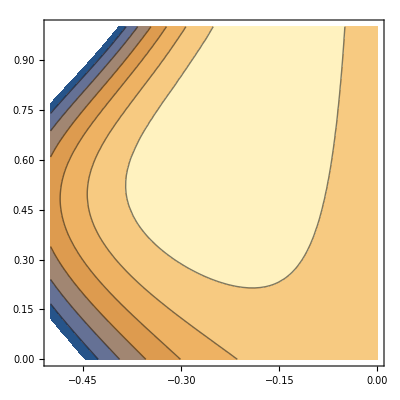

```mathematica
{c1,c2,c3,c4,c5,c6,c7}=Round[rep1[[1]]*0.0001]; (*We can get a plot if we divide the entire dataset by 10000...*)
ContourPlot[Log[Lik[s,h]],{s,0,-0.5},{h,0,1}]
```